ILUM = (∫^∞)_e_th de 1/((σ_r-e)^2+σ_i^2)·1/((a_n-e)^2+b_n^2)

```mathematica
ClearAll;
ILnum[sr_,si_,a_,b_,eth_]:=NIntegrate[1/((sr-e)^2+si^2) 1/((a-e)^2+b^2),{e,eth,Infinity}]
ILana[sr_,si_,a_,b_,eth_,c_]:=c^2/(((sr-a)^2+(si-b)^2) ((sr-a)^2+(si+b)^2)) (((sr-a)^2+b^2-si^2)/si (Pi/2+ArcTan[(sr-eth)/si])+((sr-a)^2-b^2+si^2)/b (Pi/2+ArcTan[(a-eth)/b])+(sr-a) Log[((sr-eth)^2+si^2)/((a-eth)^2+b^2)])
Lorentz[e_,a_,b_,c_]:=c^2/((a-e)^2+b^2);
GaussX[x_,c_,a_,xo_]:=c Exp[-a (x-xo)^2];
```

Consistency between numerical and analytical integration

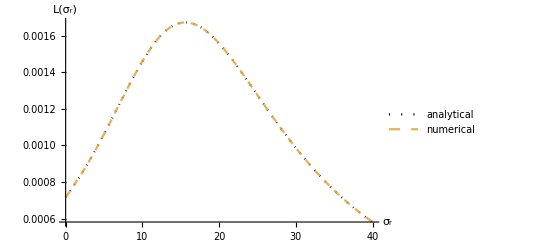

```mathematica
βtest=12.0;
γtest=12.0;
δtest=6.0;
e0test=10;
obnd=40;
Plot[{ILana[α,βtest,γtest,δtest,e0test,1.0],ILnum[α,βtest,γtest,δtest,e0test]},{α,0,obnd},PlotRange->Full,AxesLabel->{"σ_r","L(σ_r)"}, PlotStyle->{{Dotted,Black},{Dashed,Opacity[0.8]}},PlotLegends->{"analytical","numerical"}]
```

Fit model to “toy” LIT

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

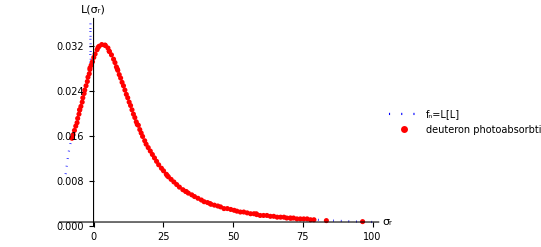

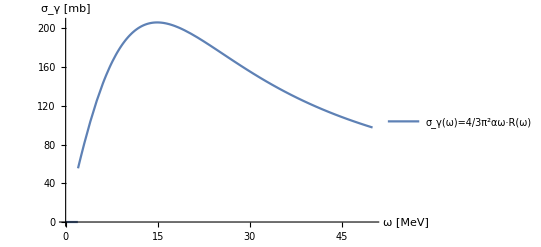

```mathematica
e0=2;si=5;
smin=-10;smax=100;bassdim=15;
toyLIT=Import["/home/kirscher/kette_repo/ComptonLIT/deuteron_toy_lit.csv"];

(*minW=3;maxW=12;
minLoc=-1;maxLoc=10;
aset=Range[minLoc,maxLoc,(maxLoc-minLoc)/bassdim];
bset=Range[minW,maxW,(maxW-minW)/bassdim];*)
modelLorentzABC=Sum[ILana[srLn,si,aLn@i,bLn@i,e0,cLn@i],{i,bassdim}];
nlmLABC=NonlinearModelFit[toyLIT,modelLorentzABC,Flatten[Table[{{aLn@i,0.01},{bLn@i,1.01},{cLn@i,0.001}},{i,bassdim}],1],srLn];

Show[
Plot[{nlmLABC[x]},{x,smin,smax},PlotStyle->{{Blue,Dotted}},PlotLegends->{"f_n=L[L]"},PlotRange->Full,AxesLabel->{"σ_r","L(σ_r)"}],
ListPlot[toyLIT,PlotLegends->{"deuteron photoabsorbtion L_γ^d(σ_r)"},PlotStyle->{Red}]
]
modelResponse[e_]:=0.1 197^2 4/3 Pi^2/137 e HeavisideTheta[e-e0] Sum[Lorentz[e,aLn@i,bLn@i,cLn@i],{i,bassdim}]/.nlmLABC["BestFitParameters"];
Plot[modelResponse[e],{e,0,50},PlotRange->{Automatic,Automatic},PlotLegends->{"σ_γ(ω)=4/3π^2αω·R(ω)"},AxesLabel->{"ω [MeV]","σ_γ [mb]"}]
nlmLABC["BestFitParameters"];
```

Construct LIT from known σ

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

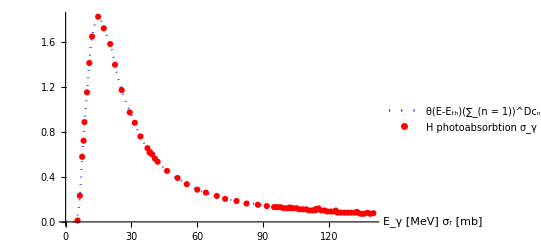

```mathematica
toyCross=Import["/home/kirscher/kette_repo/ComptonLIT/triton_inclusive_photo_abs.csv"];
guassdim=10;

modelGuass=Sum[GaussX[eGn,cGn@i,aGn@i,xoGn@i],{i,guassdim}];nlmG=NonlinearModelFit[toyCross,modelGuass,Flatten[Table[{{cGn@i,0.1},{aGn@i,0.01},{xoGn@i,10.1}},{i,guassdim}],1],eGn];
modelCross[e_]:=HeavisideTheta[e-toyCross[[1]][[1]]] Sum[GaussX[e,cGn@i,aGn@i,xoGn@i],{i,guassdim}]/.nlmG["BestFitParameters"];
CrossLit[sr_,si_]:=NIntegrate[1/((sr-e)^2+si^2) modelCross[e],{e,-Infinity,Infinity}];

emin=0.0;emax=140;
Show[
(*Plot[{nlmG[x]},{x,emin,emax},PlotStyle->{{Blue,Dotted}},PlotLegends->{"(∑_(n = 1))^dc_n^*·e^(-SubsuperscriptBox[a, n, *]SuperscriptBox[(E - SubsuperscriptBox[b, n, *]), 2])"},PlotRange->Full,AxesLabel->{"E_γ [MeV]""σ_r [mb]"}],*)
Plot[{modelCross[x]},{x,emin,emax},PlotStyle->{{Blue,Dotted}},PlotLegends->{"θ(E-E_th)(∑_(n = 1))^Dc_n^*·e^(-SubsuperscriptBox[a, n, *] SuperscriptBox[(E - SubsuperscriptBox[b, n, *]), 2])"},PlotRange->Full,AxesLabel->{"E_γ [MeV]""σ_r [mb]"}],
ListPlot[toyCross,PlotLegends->{"H photoabsorbtion σ_γ"},PlotStyle->{Red}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {5.40064}. NIntegrate obtained 0.0541203 and 1.80956×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {5.40064}. NIntegrate obtained 0.0607071 and 1.97942×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {5.40064}. NIntegrate obtained 0.0685106 and 2.17575×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {5.40064}. NIntegrate obtained 0.0541354 and 1.80995×10^-6 for the integral and error estimates.

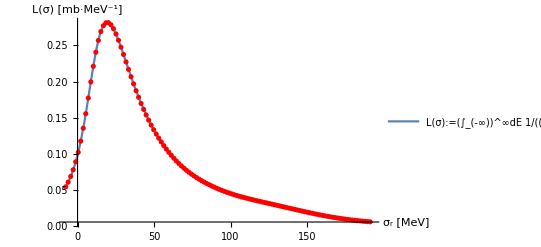

```mathematica
si=10;
nbrS=Length[toyLIT[[All,1]]];
ub=2 toyLIT[[All,1]][[-1]];
lb=toyLIT[[All,1]][[1]];
sStellen=Range[lb,ub,(ub-lb)/nbrS];

dataCrossLit=Table[{sStellen[[n]],CrossLit[sStellen[[n]],si]},{n,1,nbrS}];
Show[
Plot[CrossLit[sr,si],{sr,lb,ub},PlotLegends->{"L(σ):=(∫_(-∞))^∞dE 1/(SubscriptBox[σ, r] - E)^2·θ(E-E_th)(∑_(n = 1))^Dc_n^*·e^(-SubsuperscriptBox[a, n, *] SuperscriptBox[(E - SubsuperscriptBox[b, n, *]), 2])"},PlotRange->Full,AxesLabel->{"σ_r [MeV]","L(σ) [mb·MeV^-1]"}],
ListPlot[dataCrossLit,PlotStyle->{Red}]
]
```

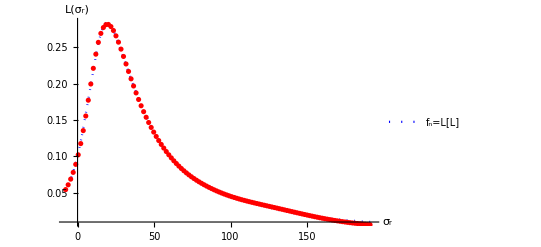

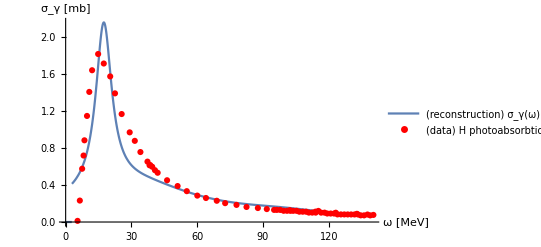

General::munfl: Exp[-4984.19] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5043.02] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3926.58] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
aLnb[1] | -206168. | 2.31766×10^7 | -0.0088955 | 0.992922
bLnb[1] | 238963. | 1.53221×10^7 | 0.015596 | 0.98759
cLnb[1] | 2.48875×10^-16 | 2.2234×10^7 | 1.11934×10^-23 | 1
aLnb[2] | 807414. | 1.67751×10^6 | 0.481317 | 0.631434
bLnb[2] | 92605.8 | 6.53369×10^6 | 0.0141736 | 0.988722
cLnb[2] | -0.0064791 | 1.83635×10^11 | -3.52825×10^-14 | 1
aLnb[3] | 398988. | 771838. | 0.516932 | 0.606444
bLnb[3] | -330034. | 655262. | -0.503667 | 0.615699
cLnb[3] | 7.33883×10^-15 | 167687. | 4.37649×10^-20 | 1
aLnb[4] | 30.8254 | 4.78993 | 6.43547 | 5.4695×10^-9
bLnb[4] | -36.073 | 1.6885 | -21.3639 | 1.96322×10^-37
cLnb[4] | 23.1498 | 3.97817 | 5.8192 | 8.53284×10^-8
aLnb[5] | -264.526 | 8.39413×10^-23 | -3.15132×10^24 | 0.
bLnb[5] | -43227.5 | 7.23742×10^-21 | -5.97278×10^24 | 0.
cLnb[5] | -1.76787×10^-16 | 1.7698 | -9.98908×10^-17 | 1
aLnb[6] | -165916. | 5.17549×10^-15 | -3.20579×10^19 | 0.
bLnb[6] | 46729.4 | 1.45558×10^-15 | 3.21037×10^19 | 0.
cLnb[6] | -1.21566×10^-12 | 763.329 | -1.59257×10^-15 | 1
aLnb[7] | 98.5429 | 4.76738 | 20.6702 | 2.4367×10^-36
bLnb[7] | 31.7773 | 8.79845 | 3.61169 | 0.000495312
cLnb[7] | 8.06604 | 2.88312 | 2.79768 | 0.00626877
aLnb[8] | 36486.7 | 4.51392 | 8083.15 | 5.69733×10^-271
bLnb[8] | 668431. | 83.2572 | 8028.5 | 1.06341×10^-270
cLnb[8] | 0.00115631 | 4.82704×10^10 | 2.39548×10^-14 | 1
aLnb[9] | -149576. | 0.00422758 | -3.5381×10^7 | 0.
bLnb[9] | -224107. | 0.00632343 | -3.54408×10^7 | 0.
cLnb[9] | -2.82231×10^-6 | 7.26525×10^8 | -3.88467×10^-15 | 1
aLnb[10] | 17.383 | 0.306165 | 56.7767 | 2.05701×10^-73
bLnb[10] | 4.38539 | 1.42547 | 3.07645 | 0.00275915
cLnb[10] | 5.87145 | 1.94096 | 3.02502 | 0.00322277

```mathematica
e0=2.84;

bassdim=10;
si=10;
modelLorentzABCb=Sum[ILana[srLnb,si,aLnb@i,bLnb@i,e0,cLnb@i],{i,bassdim}];
nlmLABCb=NonlinearModelFit[dataCrossLit,modelLorentzABCb,Flatten[Table[{{aLnb@i,RandomReal[{0.1,0.4}]},{bLnb@i,RandomReal[{2.8,15.4}]},{cLnb@i,RandomReal[{0.01,0.02}]}},{i,bassdim}],1],srLnb,Method->"LevenbergMarquardt"];
modelResponseb[e_]:=HeavisideTheta[e-e0] Sum[Lorentz[e,aLnb@i,bLnb@i,cLnb@i],{i,bassdim}]/.nlmLABCb["BestFitParameters"];

Show[
Plot[{nlmLABCb[x]},{x,lb,ub},PlotStyle->{{Blue,Dotted}},PlotLegends->{"f_n=L[L]"},PlotRange->Full,AxesLabel->{"σ_r","L(σ_r)"}],
ListPlot[dataCrossLit,PlotStyle->{Red},PlotLegends->"Gaussian LIT data"]
]

Show[
Plot[modelResponseb[e],{e,emin,emax},PlotRange->Full,PlotLegends->{"(reconstruction) σ_γ(ω)=4/3π^2αω·R(ω)"},AxesLabel->{"ω [MeV]","σ_γ [mb]"}],
ListPlot[toyCross,PlotLegends->{"(data) H photoabsorbtion σ_γ"},PlotStyle->{Red}]
]
nlmLABCb["ParameterTable"]
```